```mathematica
(*P7.8*)
(*A*)
eq=x^2*D[f[x],{x,2}]+x D[f[x],x]+(x^2-n^2)*f[x]==0;
DSolve[eq,f[x],x]
```

{{f[x]→BesselJ[n,x] C[1]+BesselY[n,x] C[2]}}

```mathematica
(*B*)
eq=(1-x^2)*D[f[x],{x,2}]-2x D[f[x],x]+n(n+1)f[x]==0;
DSolve[eq,f[x],x]
```

{{f[x]→C[1] LegendreP[n,x]+C[2] LegendreQ[n,x]}}

InterpolatingFunction[…][x]

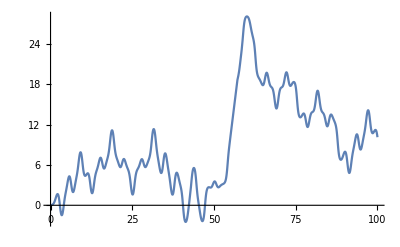

```mathematica
(*P7.9*)
(*A*)
Clear["`*"]
eq={v[x]==y'[x],v'[x]==10Sin[y[x]]*Cos[x],y[0]==0,v[0]==.1};
sol[x_]=NDSolveValue[eq,{y[x],v[x]},{x,0,100}][[1]]
Plot[sol[x],{x,0,100}]
```